```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
```

## Definitions

```mathematica
kfinal={0.4709613222916442,-0.2550225519531524};
kfinalu={0.8020780608066254,-0.360468820434673};
kfinall={0.13984458377666326,-0.14957628347163182};
αcont={0.5137193759431391,0.0024666827878353577}; 
σcont={0.16955497884544793,0.0008581023195660334};
ccont={-0.15956635071361625,0.0024752900407607015};
```

```mathematica
mDcal[T_,c_,d_]:=Re[Sqrt[Nc/3+nF/6]g4[2π T]T+1/(4π)Nc g4[2π T]^2 T Log[Sqrt[Nc/3+nF/6]/g4[2π T]]+c g4[2π T]^2 T+d g4[2π T]^3 T ];
```

### 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

### Self Energies & Potential

#### v = 0

```mathematica
g[x_]:=Quiet[2NIntegrate[p/(p^2+1)Sinc[p x],{p,0,∞}]];
ϕ[x_]:=Quiet[2NIntegrate[z/((z^2+1)^2)(1-Sinc[x z]),{z,0,∞}]];
ψ[r_,m_,α_,σ_]:=Re[ParabolicCylinderD[-1/2,0]NIntegrate[ParabolicCylinderD[-1/2,√2 y] y^2 g[y m/((m^2 σ/α)^(1/4))],{y,0,∞}]]-ParabolicCylinderD[-1/2,√2 r]NIntegrate[y^2 g[y m/((m^2 σ/α)^(1/4))]Re[ParabolicCylinderD[-1/2,ⅈ √2 y]],{y,0,r}]-Re[ParabolicCylinderD[-1/2,ⅈ √2 r]]NIntegrate[ParabolicCylinderD[-1/2,√2 y] y^2 g[y m/((m^2 σ/α)^(1/4))],{y,r,∞}];
```

```mathematica
ReV0[r_,m_,α_,σ_,c_]:=-α m-α Exp[-m r]/r-Gamma[1/4]/(2^(3/4)√π)σ/((m^2 σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(m^2 σ/α)^(1/4) r]+Gamma[1/4]/(2Gamma[3/4])σ/((m^2 σ/α)^(1/4))+c;
ImV0[r_,m_,α_,σ_,T_]:=α T ϕ[m r]+α T ψ[(m^2 σ/α)^(1/4) r,m,α,σ];
```

#### v =/= 0

```mathematica
Πpar[θ_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[θ]^2 Sin[θ]^2)/((1-v^2 Sin[θ]^2)^2)-((2+v^2 Sin[θ]^2)(1-v^2)v Cos[θ])/(2(1-v^2 Sin[θ]^2)^(5/2))Log[(v Cos[θ]+√(1-v^2 Sin[θ]^2))/(v Cos[θ]-√(1-v^2 Sin[θ]^2))]);
Πper[θ_,β_,v_,mD_]:=mD^2/2((2-2 v^2-v^4 Cos[β]^2 Sin[θ]^2(1-Cos[β]^2 Sin[θ]^2))/((1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)-((2+v^2-v^2 Cos[β]^2 Sin[θ]^2)(1-v^2)v Cos[β]Sin[θ])/(2(1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^2)Log[(v Cos[β]Sin[θ]+√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))/(v Cos[β]Sin[θ]-√(1-v^2+v^2 Cos[β]^2 Sin[θ]^2))]);
```

```mathematica
ImVcpar[r_,θ_,v_,mD_,T_,α_]:=α T mD^2 ((1-v^2)^(3/2)(2+v^2 Sin[θ]^2))/((1-v^2 Sin[θ]^2)^(5/2))NIntegrate[p/((p^2+Πpar[θ,v,mD])(p^2+Conjugate[Πpar[θ,v,mD]]))(1-Sinc[p r]),{p,0,∞}];
ImVcper[r_,θ_,β_,v_,mD_,T_,α_]:=α mD^2 T((1-v^2)^(3/2)(2+v^2-v^2 Cos[β]^2 Sin[θ]^2))/((1-v^2+v^2 Cos[β]^2 Sin[θ]^2)^(5/2))NIntegrate[p/((p^2+Πper[θ,β,v,mD])(p^2+Conjugate[Πper[θ,β,v,mD]]))(1-Sinc[p r]),{p,0,∞}];
```

```mathematica
ReVcpar[r_,θ_,v_,mD_,T_,α_]:=-α Exp[-√Πpar[θ,v,mD]r]/r-α √Πpar[θ,v,mD];
ReVcper[r_,θ_,β_,v_,mD_,T_,α_]:=-α Exp[-√Πper[θ,β,v,mD]r]/r-α √Πper[θ,β,v,mD];
```

```mathematica
ReVspar[r_,θ_,v_,mD_,T_,α_,σ_]:=-(Gamma[1/4]σ)/(2^(3/4)√π(Πpar[θ,v,mD] σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(Πpar[θ,v,mD] σ/α)^(1/4)r]+(Gamma[1/4]σ)/(2Gamma[3/4](Πpar[θ,v,mD] σ/α)^(1/4));
ReVsper[r_,θ_,β_,v_,mD_,T_,α_,σ_]:=-(Gamma[1/4]σ)/(2^(3/4)√π(Πper[θ,β,v,mD] σ/α)^(1/4))ParabolicCylinderD[-1/2,√2(Πper[θ,β,v,mD] σ/α)^(1/4)r]+(Gamma[1/4]σ)/(2Gamma[3/4](Πper[θ,β,v,mD] σ/α)^(1/4));
```

```mathematica
gpar[r_,θ_,v_,mD_]:=NIntegrate[2 z/(z^2+1/mD^2 Conjugate[Πpar[θ,v,mD]])Sinc[z r],{z,0,∞}];
gper[r_,θ_,β_,v_,mD_]:=NIntegrate[2 z/(z^2+1/mD^2 Conjugate[Πper[θ,β,v,mD]])Sinc[z r],{z,0,∞}];
```

```mathematica
ψpar[x_,θ_,v_,mD_,α_,σ_]:=ParabolicCylinderD[-1/2,√2 x]NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 y]] y^2 gpar[(y mD)/(Πpar[θ,v,mD] σ/α)^(1/4),θ,v,mD],{y,0,x}]+Re[ParabolicCylinderD[-1/2,ⅈ √2 x]]NIntegrate[ParabolicCylinderD[-1/2,√2 y] y^2 gpar[(y mD)/(Πpar[θ,v,mD] σ/α)^(1/4),θ,v,mD],{y,x,∞}]-ParabolicCylinderD[-1/2,0]NIntegrate[ParabolicCylinderD[-1/2,√2 y] y^2 gpar[(y mD)/(Πpar[θ,v,mD] σ/α)^(1/4),θ,v,mD],{y,0,∞}];
ψper[x_,θ_,β_,v_,mD_,α_,σ_]:=ParabolicCylinderD[-1/2,√2 x]NIntegrate[Re[ParabolicCylinderD[-1/2,ⅈ √2 y]] y^2 gper[(y mD)/(Πper[θ,β,v,mD] σ/α)^(1/4),θ,β,v,mD],{y,0,x}]+Re[ParabolicCylinderD[-1/2,ⅈ √2 x]]NIntegrate[ParabolicCylinderD[-1/2,√2 y] y^2 gper[(y mD)/(Πper[θ,β,v,mD] σ/α)^(1/4),θ,β,v,mD],{y,x,∞}]-ParabolicCylinderD[-1/2,0]NIntegrate[ParabolicCylinderD[-1/2,√2 y] y^2 gper[(y mD)/(Πper[θ,β,v,mD] σ/α)^(1/4),θ,β,v,mD],{y,0,∞}];
```

```mathematica
ImVspar[r_,θ_,v_,mD_,T_,α_,σ_]:=-(α T mD^2)/Πpar[θ,v,mD]ψpar[(Πpar[θ,v,mD] σ/α)^(1/4)r,θ,v,mD,α,σ];
ImVsper[r_,θ_,β_,v_,mD_,T_,α_,σ_]:=-(α T mD^2)/Πper[θ,β,v,mD]ψper[(Πper[θ,β,v,mD] σ/α)^(1/4)r,θ,β,v,mD,α,σ];
```

### Consistency checks

```mathematica
mD=mDcal[0.155,kfinal[[1]],kfinal[[2]]]
```

0.148564

```mathematica
√Πpar[θ,0.,mD]
```

0.148564+0. ⅈ

```mathematica
√Πper[θ,β,0.,mD]
```

0.148564+0. ⅈ

```mathematica
ImVcpar[5,θ,0.,mD,0.155,αcont[[1]]]+ImVspar[5,θ,0.,mD,0.155,αcont[[1]],σcont[[1]]]
```

NIntegrate::inumr: The integrand (2 z Sinc[(0.508522+0. ⅈ) y z])/((1.+0. ⅈ)+z^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.0441988+0. ⅈ

```mathematica
ImVcper[5,θ,ϕ1,β,0.,mD,0.155,αcont[[1]]]+ImVsper[5,θ,ϕ1,β,0.,mD,0.155,αcont[[1]],σcont[[1]]]
```

NIntegrate::inumr: The integrand (2 z Sinc[(0.508522+0. ⅈ) y z])/((1.+0. ⅈ)+z^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

0.0441988+0. ⅈ

```mathematica
Quiet[ImV0[5,mD,αcont[[1]],σcont[[1]],0.155]]
```

0.044197

```mathematica
ReVcpar[5.,θ,0.,mD,0.155,αcont[[1]]]+ReVspar[5.,θ,0.,mD,0.155,αcont[[1]],σcont[[1]]]+ccont[[1]]
```

0.4154+0. ⅈ

```mathematica
ReVcper[5.,θ,ϕ1,β,0.,mD,0.155,αcont[[1]]]+ReVsper[5.,θ,ϕ1,β,0.,mD,0.155,αcont[[1]],σcont[[1]]]+ccont[[1]]
```

0.4154+0. ⅈ

### Plotting

```mathematica
mD=mDcal[0.155,kfinal[[1]],kfinal[[2]]];
```

```mathematica
ReVper[r_,θ_,β_,v_,mD_,T_,α_,σ_,c_]:=Re[ReVcper[r,θ,β,v,mD,T,α]+ReVsper[r,θ,β,v,mD,T,α,σ]+c];
```

```mathematica
ImVper[r_,θ_,β_,v_,mD_,T_,α_,σ_]:=Quiet[Im[ImVcper[r,θ,β,v,mD,T,α]+ImVsper[r,θ,β,v,mD,T,α,σ]]];
```

```mathematica
(*we want to simulate many collisions at a given v by calculating averaged quantites over β∈[0,π/4] and θ∈[0,pi]*)
```

```mathematica
ReVper[6,0,0,0.9,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]]
ReVper[6,0,π/5,0.9,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]]
```

0.214189

0.214189

```mathematica
ImVper[6,0,0,0.9,mD,0.155,αcont[[1]],σcont[[1]]]
ImVper[6,0,π/5,0.9,mD,0.155,αcont[[1]],σcont[[1]]]
```

0.

0.

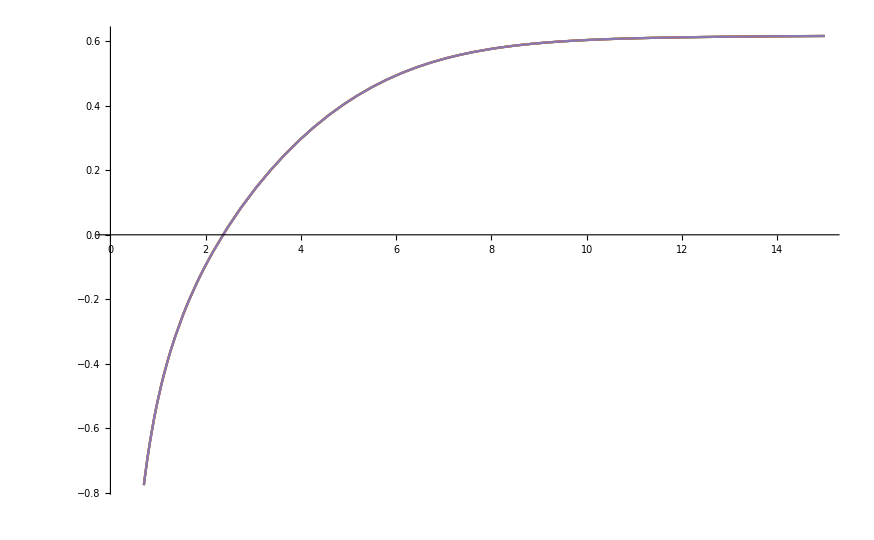

```mathematica
Plot[{ReVper[r,0,0,0.1,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]],ReVper[r,0,π/16,0.1,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]],ReVper[r,0,π/8,0.1,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]],ReVper[r,0,3π/16,0.1,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]],ReVper[r,0,2π,0.1,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0,15}]
```

### Spectra

```mathematica
swaveccspectra[v_]:=Module[{mD=mDcal[0.155,kfinal[[1]],kfinal[[2]]],σ=σcont[[1]],α=αcont[[1]],c=ccont[[1]],M=1.4690612135716832,l=0,ρtable,ccsT,ϵ=1/1000,pg=1,rat,μ,δ,Imtable,dω,ω,ωmin,ωmax,inf,gr,gr0,s01,rho,s1,rhow,iminter,pot,rev},
μ=(mD^2 σ/α)^(1/4);
rat=mD/μ;
Imtable=Join[Parallelize[Table[{x,Quiet[ImVper[x,0,0,π/4,v,mD,0.155,αcont[[1]],σcont[[1]]]]},{x,ϵ/100,1,10ϵ}]],Parallelize[Table[{x,Quiet[ImVper[x,0,0,π/4,v,mD,0.155,αcont[[1]],σcont[[1]]]]},{x,1+100ϵ,10+ϵ,100ϵ}]],Parallelize[Table[{x,Quiet[ImVper[x,0,0,π/4,v,mD,0.155,αcont[[1]],σcont[[1]]]]},{x,11,100,1}]],Parallelize[Table[{x,Quiet[ImVper[x,0,0,π/4,v,mD,0.155,αcont[[1]],σcont[[1]]]]},{x,200,1000,100}]],Parallelize[Table[{x,Quiet[ImVper[x,0,0,π/4,v,mD,0.155,αcont[[1]],σcont[[1]]]]},{x,2000,20000,1000}]]];

rev=Interpolation[Join[Table[{r,ReVper[r,0,0,π/4,v,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,0.001,10,0.01}],Table[{r,ReVper[r,0,0,π/4,v,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,10.1,25,0.1}],Table[{r,ReVper[r,0,0,π/4,v,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,26,1000,1}],Table[{r,ReVper[r,0,0,π/4,v,mD,0.155,αcont[[1]],σcont[[1]],ccont[[1]]]},{r,1010,20000,10}]]];

iminter=Interpolation[Imtable,InterpolationOrder->1];
pot[x_]:=rev[x]+ⅈ iminter[x];

δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=2;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω M}];
SetSharedVariable[ρtable]

ParallelDo[ω=ωmin+(it-1) dω M;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[pot[r]]+ⅈ Abs[Im[pot[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==(α M)-δ(M α)^2,
 gr[δ]==δ(α M)- 1/2 δ^2(α M)^2},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc M^2 α)/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2M,rhow[inf]},{it,1,Length[ρtable]}];

ccsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];
Export["spectraldata/Vscan/cc/swccv"<>ToString[v]<>"spectra.dat",ccsT]
]
```

```mathematica
swaveccspectra[0.1]//AbsoluteTiming
```

{915.364,spectraldata/Vscan/cc/swccv0.1spectra.dat}

```mathematica
swaveccspectra[0.2]//AbsoluteTiming
```

{939.577,spectraldata/Vscan/cc/swccv0.2spectra.dat}

```mathematica
swaveccspectra[0.3]//AbsoluteTiming
```

{875.422,spectraldata/Vscan/cc/swccv0.3spectra.dat}

```mathematica
swaveccspectra[0.4]//AbsoluteTiming
```

{919.588,spectraldata/Vscan/cc/swccv0.4spectra.dat}

```mathematica
swaveccspectra[0.5]//AbsoluteTiming
```

{949.731,spectraldata/Vscan/cc/swccv0.5spectra.dat}

```mathematica
swaveccspectra[0.6]//AbsoluteTiming
```

{884.336,spectraldata/Vscan/cc/swccv0.6spectra.dat}

```mathematica
swaveccspectra[0.7]//AbsoluteTiming
```

{908.082,spectraldata/Vscan/cc/swccv0.7spectra.dat}

```mathematica
swaveccspectra[0.8]//AbsoluteTiming
```

{998.753,spectraldata/Vscan/cc/swccv0.8spectra.dat}

```mathematica
swaveccspectra[0.9]//AbsoluteTiming
```

{878.394,spectraldata/Vscan/cc/swccv0.9spectra.dat}